# 正态分布函数

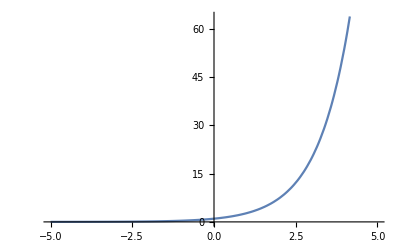

```mathematica
Plot[Exp[x],{x,-5,5}]
```

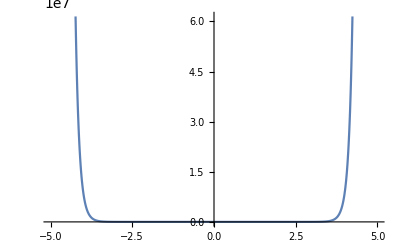

```mathematica
Plot[Exp[x^2],{x,-5,5}]
```

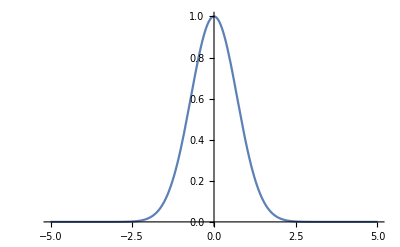

```mathematica
Plot[Exp[-x^2],{x,-5,5}]
```

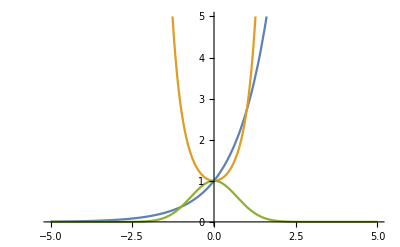

```mathematica
Plot[{Exp[x],Exp[x^2],Exp[-x^2]},{x,-5,5},PlotRange->{{-5,5},{0,5}}]
```

```mathematica
Integrate[Exp[-x^2],{x,-∞,∞}]
```

√π

```mathematica
Integrate[1/(√π)Exp[-x^2],{x,-∞,∞}]
```

1

```mathematica
Integrate[1/(√π)Exp[-x^2/a],{x,-∞,∞},Assumptions->a>0]
```

√a

```mathematica
Integrate[1/(√π σ)Exp[-(x-μ)^2/σ^2],{x,-∞,∞},Assumptions->σ>0]
```

1

```mathematica
Integrate[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,-∞,∞},Assumptions->σ>0]
```

1

```mathematica
Manipulate[Show[Plot[1/(√(2π)σ)E^(-(x-μ)^2/(2 σ^2)),{x,-5,5}],Graphics[{Magenta,Dashed,Line[{{μ,-1},{μ,5}}]}]],{{μ,1},-5,5},{{σ,1},0.0001,5}]
```